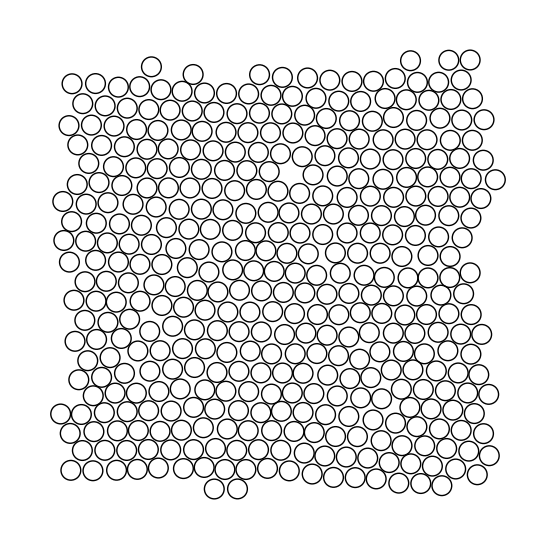

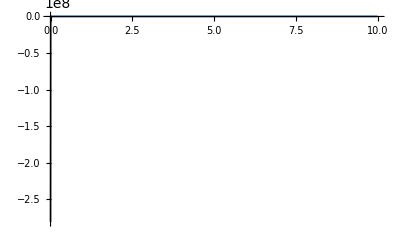

```mathematica
dataall=Import["/home/jiahaoz/Desktop/mse3/project5/info.txt","Table"];
Graphics@Table[Circle[dataall[[i]],1.7*10^-10],{i,1,Length[dataall]}]
```

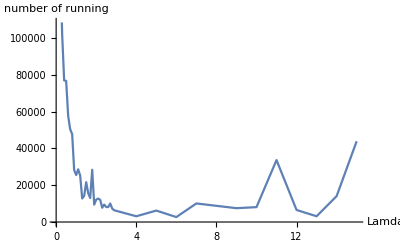
```mathematica
dataall=Import["time.txt","Table"];
ListLinePlot[dataall,AxesLabel->{"Lamda","number of running"}]
-Graphics-
```

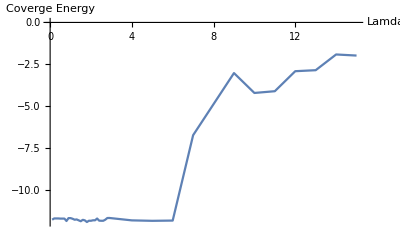

```mathematica
dataall=Import["ener.txt","Table"];
ListLinePlot[dataall,AxesLabel->{"Lamda","Coverge Energy"}]
```

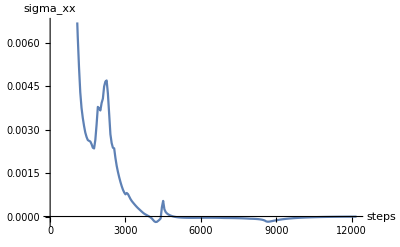

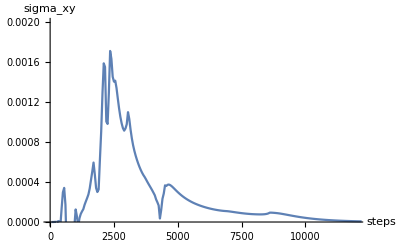

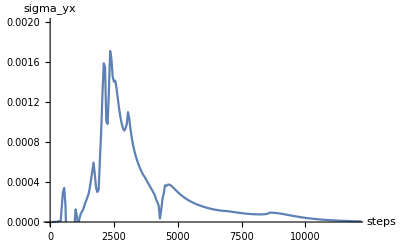

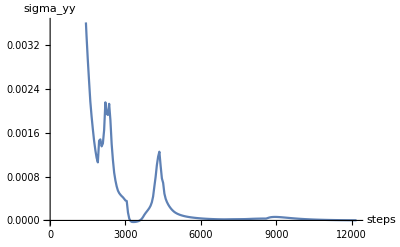

```mathematica
dataall=Import["stress.txt","Table"];
data=dataall[[1;;-3]];
steps=data[[;;,1]];
sigmaxx=data[[;;,2]];
sigmaxy=data[[;;,3]];
sigmayx=data[[;;,4]];
sigmayy=data[[;;,5]];
ListLinePlot[Table[{steps[[i]],sigmaxx[[i]]},{i,1,Length[steps]}],AxesLabel->{"steps","sigma_xx"}]
ListLinePlot[Table[{steps[[i]],sigmaxy[[i]]},{i,1,Length[steps]}],AxesLabel->{"steps","sigma_xy"},PlotRange->{{0,12000},{0,0.002}}]
ListLinePlot[Table[{steps[[i]],sigmayx[[i]]},{i,1,Length[steps]}],AxesLabel->{"steps","sigma_yx"},PlotRange->{{0,12000},{0,0.002}}]
ListLinePlot[Table[{steps[[i]],sigmayy[[i]]},{i,1,Length[steps]}],AxesLabel->{"steps","sigma_yy"}]
```

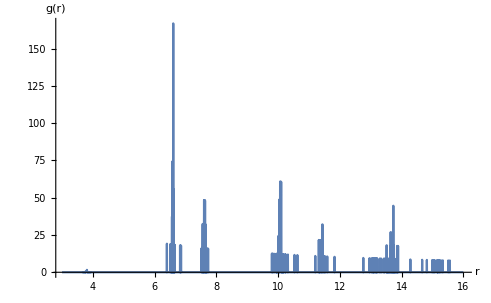

```mathematica
dataall=Import["radial.txt","Table"];
data=dataall[[2;;-1]];
ListLinePlot[data,AxesLabel->{"r","g(r)"}]
```

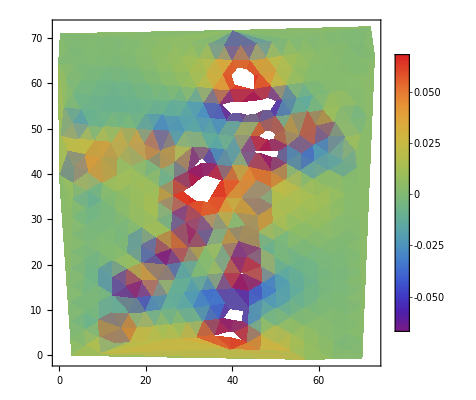

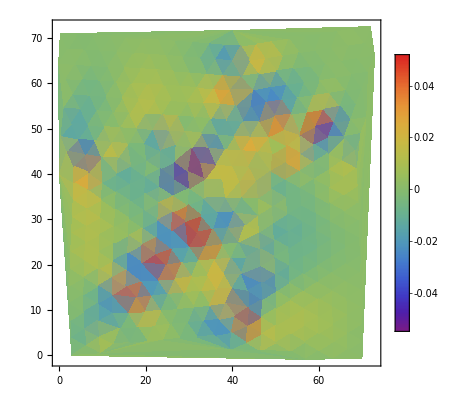

-Graphics-

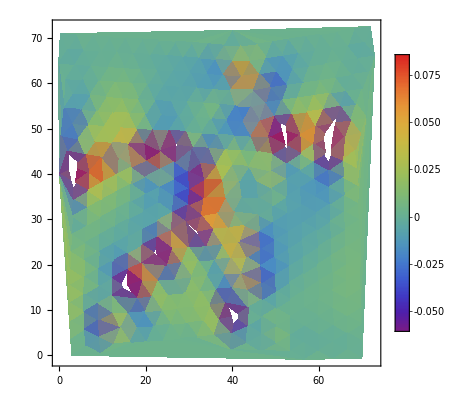

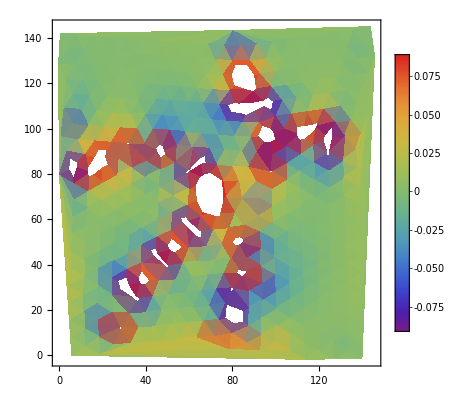

```mathematica
ClearAll[datastress]
datastress=Import["stress_xx.txt","Table"];
stressxx=Table[{datastress[[i,1]],datastress[[i,2]],datastress[[i,3]]},{i,1,400}];
stressxy=Table[{datastress[[i,1]],datastress[[i,2]],datastress[[i,4]]},{i,1,400}];
stressyx=Table[{datastress[[i,1]],datastress[[i,2]],datastress[[i,5]]},{i,1,400}];
stressyy=Table[{datastress[[i,1]],datastress[[i,2]],datastress[[i,6]]},{i,1,400}];
ListDensityPlot[stressxx,ColorFunction->"Rainbow",PlotLegends->Automatic]
ListDensityPlot[stressxy,ColorFunction->"Rainbow",PlotLegends->Automatic]
ListDensityPlot[stressyx,ColorFunction->"Rainbow",PlotLegends->Automatic]
ListDensityPlot[stressyy,ColorFunction->"Rainbow",PlotLegends->Automatic]
ListDensityPlot[stressyy+stressxx,ColorFunction->"Rainbow",PlotLegends->Automatic]
```